Evaluate the initialization cells in numericalMaximization.nb before using this notebook.

Use partialEvolution to compute the output projected state after a given number of steps. This function can be used to see how the walker evolves before generating a target state.

```mathematica
partialEvolution[results_Association,nSteps_Integer]:=Module[{shorterResults=results},
shorterResults["CoinParameters"]=(shorterResults["CoinParameters"]//DeleteCases[_[n_/;n>nSteps]->_]);
searchResultComputeProjectedOutput@shorterResults
];
```

```mathematica
seeEvolutionByStep[results_Association]:=With[{
nSteps=Length@results["TargetState"]-1
},
Manipulate[
partialEvolution[results,nStep]//normalizePhase//ListPlot[
{
Transpose@{Range@Length@#,Re@#},
Transpose@{Range@Length@#,Im@#}
},
PlotRange->{{0.9,nSteps+1.1},All},
Joined->True,PlotMarkers->Automatic
]&,
{{nStep,nSteps},1,nSteps,1,Appearance->"Labeled"}
]
];
```

Focus on six-site walker sites

## Focus on two different sites

```mathematica
ClearAll@searchCoinParameters`Cache
target=N@{1,1,0,0,0,0};
results=searchCoinParameters[5,Normalize@target,"IncludeProjectionInMaximization"->False,
WorkingPrecision->20
]
Echo[#,"Projection probability: "]&@searchResultProjectionProbability@results;
DynamicModule[{data=results},seeEvolutionByStep@results]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→1.000000000000000222,CoinParameters→{θ[1]→-3.1843497771847109848×10^-15,ξ[1]→6.4789384117881543028,θ[2]→-8.8880966073743894971×10^-16,ξ[2]→-5.0925308266891191129,θ[3]→1.3025985001946431029×10^-14,ξ[3]→3.3908804781091705624,θ[4]→-1.8889191023943980159×10^-14,ξ[4]→-0.40175793252852214279,θ[5]→-0.7853981633974590821,ξ[5]→-1.1926386741815360086×10^-14},TargetState→{0.707107,0.707107,0.,0.,0.,0.}|>

Projection probability:  0.49999999999999131

```mathematica
ClearAll@searchCoinParameters`Cache
target=N@{1,0,1,0,0,0};
results=searchCoinParameters[5,Normalize@target,"IncludeProjectionInMaximization"->False,
WorkingPrecision->20
]
Echo[#,"Projection probability: "]&@searchResultProjectionProbability@results;
DynamicModule[{data=results},seeEvolutionByStep@results]
```

{1.,0.,1.,0.,0.,0.}

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→1.000000000000000222,CoinParameters→{θ[1]→-7.3239392217264324875×10^-15,ξ[1]→0.26442210631690113308,θ[2]→4.3832893539376693229×10^-11,ξ[2]→0.37813310496633499891,θ[3]→1.2480556543368562999×10^-14,ξ[3]→0.37420828833008660783,θ[4]→-0.78539816338499604091,ξ[4]→-0.16042377178789364927,θ[5]→5.0395622975844852062×10^-13,ξ[5]→0.080211885875919852755},TargetState→{0.707107,0.,0.707107,0.,0.,0.}|>

Final fidelity:  0.5000000000124593

```mathematica
ClearAll@searchCoinParameters`Cache
target=N@{1,0,0,1,0,0};
results=searchCoinParameters[5,Normalize@target,"IncludeProjectionInMaximization"->False,
WorkingPrecision->20
]
Echo[#,"Projection probability: "]&@searchResultProjectionProbability@results;
DynamicModule[{data=results},seeEvolutionByStep@results]
```

{1.,0.,0.,1.,0.,0.}

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→0.99999999999916755478,CoinParameters→{θ[1]→-6.7811290194715772353×10^-7,ξ[1]→-0.30266886091543257176,θ[2]→-8.4207246384169495509×10^-7,ξ[2]→0.7855570824489371446,θ[3]→-0.78539806166342116889,ξ[3]→0.42258481325401272894,θ[4]→1.6209530951439005595×10^-6,ξ[4]→-0.0045923187350182806237,θ[5]→1.3951291501307654582×10^-6,ξ[5]→-0.20670050206213158651},TargetState→{0.707107,0.,0.,0.707107,0.,0.}|>

Final fidelity:  0.49999999999778466

```mathematica
ClearAll@searchCoinParameters`Cache
target=N@{1,0,0,0,1,0};
results=searchCoinParameters[5,Normalize@target,"IncludeProjectionInMaximization"->False,
WorkingPrecision->20
]
Echo[#,"Projection probability: "]&@searchResultProjectionProbability@results;
DynamicModule[{data=results},seeEvolutionByStep@results]
```

{1.,0.,0.,0.,1.,0.}

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→0.99999999999999988898,CoinParameters→{θ[1]→-9.4180635825623368371×10^-16,ξ[1]→-0.9806815232757671721,θ[2]→-0.78539816339744817719,ξ[2]→1.7730376228908405486,θ[3]→2.544323329547417718×10^-15,ξ[3]→-0.84721156302985731523,θ[4]→-0.036039492055446677586,ξ[4]→-0.078614496831090531626,θ[5]→1.3298619373891920052×10^-15,ξ[5]→0.039307248415525624556},TargetState→{0.707107,0.,0.,0.,0.707107,0.}|>

Final fidelity:  0.49935

```mathematica
ClearAll@searchCoinParameters`Cache
target=N@{1,0,0,0,0,1};
results=searchCoinParameters[5,Normalize@target,"IncludeProjectionInMaximization"->False,
WorkingPrecision->20
]
Echo[#,"Projection probability: "]&@searchResultProjectionProbability@results;
DynamicModule[{data=results},seeEvolutionByStep@results]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→0.99999999999951882934,CoinParameters→{θ[1]→0.78539863887808817594,ξ[1]→0.12547016510314124846,θ[2]→-1.8299468283114026623×10^-7,ξ[2]→0.66233491352907770179,θ[3]→7.3550326745307200401×10^-8,ξ[3]→0.62896531513303029411,θ[4]→-1.2644743664071632439×10^-7,ξ[4]→-0.011387923955956529304,θ[5]→5.4882035189838060652×10^-7,ξ[5]→0.22814920002211998323},TargetState→{0.707107,0.,0.,0.,0.,0.707107}|>

Final fidelity:  0.49999999999991548

## Focus on three output modes

```mathematica
ClearAll@searchCoinParameters`Cache
target=N@{1,1,0,0,0,1};
results=searchCoinParameters[5,Normalize@target,"IncludeProjectionInMaximization"->False,
WorkingPrecision->20
]
Echo[#,"Projection probability: "]&@searchResultProjectionProbability@results;
DynamicModule[{data=results},seeEvolutionByStep@results]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→0.99999999999822275498,CoinParameters→{θ[1]→0.78539935075177708087,ξ[1]→-3.141595294275676216,θ[2]→0.57205396217756562454,ξ[2]→3.1415949054596700083,θ[3]→0.35719566674651143227,ξ[3]→-1.1851081220172408102×10^-6,θ[4]→0.32503885905322014514,ξ[4]→1.1958226177749587946×10^-7,θ[5]→-0.85240582045951110721,ξ[5]→3.9762530152065335663×10^-7},TargetState→{0.57735,0.57735,0.,0.,0.,0.57735}|>

Projection probability:  0.18103929588

```mathematica
ClearAll@searchCoinParameters`Cache
target=N@{1,1,0,-1,0,0};
results=searchCoinParameters[5,Normalize@target,"IncludeProjectionInMaximization"->False,
WorkingPrecision->20
]
Echo[#,"Projection probability: "]&@searchResultProjectionProbability@results;
DynamicModule[{data=results},seeEvolutionByStep@results]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→0.99999999999978350651,CoinParameters→{θ[1]→-2.399760595951899031×10^-7,ξ[1]→-0.56520734961667449106,θ[2]→3.7470948843167813312×10^-8,ξ[2]→0.73316093162090794095,θ[3]→0.78539856545766148512,ξ[3]→-7.9488098881101943399×10^-7,θ[4]→0.46364785788152024626,ξ[4]→6.3732967426874381155×10^-7,θ[5]→-0.78539852285961927343,ξ[5]→8.4741928392668484086×10^-8},TargetState→{0.57735,0.57735,0.,-0.57735,0.,0.}|>

Projection probability:  0.29999969379

## Other examples

```mathematica
ClearAll@searchCoinParameters`Cache
target=N@{.2,1,.2,.2,1,.2};
results=searchCoinParameters[5,Normalize@target,"IncludeProjectionInMaximization"->True,
WorkingPrecision->20
]
Echo[#,"Projection probability: "]&@searchResultProjectionProbability@results;
DynamicModule[{data=results},seeEvolutionByStep@results]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→0.99999994649713497274,CoinParameters→{θ[1]→-0.90258440767735638821,ξ[1]→-0.7010446819731450935,θ[2]→-0.35261860256637224702,ξ[2]→-0.17634668550789327902,θ[3]→-1.2038990973736844932,ξ[3]→-0.42130689757626654794,θ[4]→1.2053618589720310184,ξ[4]→0.2387255547769816073,θ[5]→0.35340178638516278848,ξ[5]→-0.86133327289340880947,α→-0.66917060259358273008},TargetState→{0.136083,0.680414,0.136083,0.136083,0.680414,0.136083}|>

Projection probability:  0.16277811084075244

```mathematica
ClearAll@searchCoinParameters`Cache
target=N@{.5,.6,.7,.8,.9,-1.};
results=searchCoinParameters[5,Normalize@target,"IncludeProjectionInMaximization"->False,
WorkingPrecision->20
]
Echo[#,"Projection probability: "]&@searchResultProjectionProbability@results;
DynamicModule[{data=results},seeEvolutionByStep@results]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→0.99999999996108290823,CoinParameters→{θ[1]→-1.1071581484985607608,ξ[1]→0.19962502744360715993,θ[2]→0.72064526290405671647,ξ[2]→2.023185320817415255,θ[3]→-0.62804042569749581082,ξ[3]→-2.3353499313650660985,θ[4]→-0.17790350955917216175,ξ[4]→2.2535405875294142794,θ[5]→-1.0917351952516739029,ξ[5]→-0.47039452749912809425},TargetState→{0.265372,0.318447,0.371521,0.424596,0.47767,-0.530745}|>

Projection probability:  0.10803903610881678

```mathematica
ClearAll@searchCoinParameters`Cache
target=N@{.5,.6,.7,.8,.9,-1.};
results=searchCoinParameters[5,Normalize@target,"IncludeProjectionInMaximization"->True,
WorkingPrecision->20
]
Echo[#,"Projection probability: "]&@searchResultProjectionProbability@results;
DynamicModule[{data=results},seeEvolutionByStep@results]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→0.99999999997193667056,CoinParameters→{θ[1]→2.2918840832945376571,ξ[1]→0.64635252416635045007,θ[2]→0.54850721434093332572,ξ[2]→-0.59922809763861153011,θ[3]→-0.14005619202709417132,ξ[3]→0.25996653654367592288,θ[4]→0.76588160813927147981,ξ[4]→0.082776713982810837378,θ[5]→0.35818317293479816138,ξ[5]→-0.066694785812310316912,α→-1.053609232793536881},TargetState→{0.265372,0.318447,0.371521,0.424596,0.47767,-0.530745}|>

Projection probability:  0.49222497286765506

## Focus on balanced outputs and other cool stuff

```mathematica
ClearAll@searchCoinParameters`Cache
target=N@{1,1,1,1,1,1};
results=searchCoinParameters[5,Normalize@target,"IncludeProjectionInMaximization"->True,
WorkingPrecision->20
]
Echo[#,"Projection probability: "]&@searchResultProjectionProbability@results;
DynamicModule[{data=results},seeEvolutionByStep@results]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→0.99999999999846722609,CoinParameters→{θ[1]→-0.90164541731680216797,ξ[1]→1.817408702296996766,θ[2]→0.39254867142252936152,ξ[2]→0.36216384230416511859,θ[3]→0.9946885875614178858,ξ[3]→-0.81651322493795954444,θ[4]→-0.99468805524819556873,ξ[4]→0.50765997650393489603,θ[5]→-0.39255067842336244894,ξ[5]→-0.96201525336995612237,α→0.66915241163033360601},TargetState→{0.408248,0.408248,0.408248,0.408248,0.408248,0.408248}|>

Projection probability:  0.091160205382747608

```mathematica
ClearAll@searchCoinParameters`Cache
target=N@{1,1,1,1,1,1};
results=searchCoinParameters[5,Normalize@target,"IncludeProjectionInMaximization"->False]
Echo[#,"Projection probability: "]&@searchResultProjectionProbability@results;
DynamicModule[{data=results},seeEvolutionByStep@results]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→-0.785398,ξ[1]→2.41366×10^-10,θ[2]→-0.810837,ξ[2]→-5.7335×10^-10,θ[3]→0.627219,ξ[3]→7.40377×10^-10,θ[4]→0.627219,ξ[4]→-5.23448×10^-10,θ[5]→-0.810837,ξ[5]→1.44611×10^-10},TargetState→{0.408248,0.408248,0.408248,0.408248,0.408248,0.408248}|>

Projection probability:  0.145182

```mathematica
ClearAll@searchCoinParameters`Cache
target=N@{1,I,1,I,1,I};
results=searchCoinParameters[5,Normalize@target,"IncludeProjectionInMaximization"->False]
Echo[#,"Projection probability: "]&@searchResultProjectionProbability@results;
DynamicModule[{data=results},seeEvolutionByStep@results]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→0.785398,ξ[1]→-2.61799,θ[2]→-0.463648,ξ[2]→2.0944,θ[3]→-0.785398,ξ[3]→0.523599,θ[4]→-0.785398,ξ[4]→-2.76078×10^-9,θ[5]→0.463648,ξ[5]→-0.523599},TargetState→{0.408248+0. ⅈ,0.+0.408248 ⅈ,0.408248+0. ⅈ,0.+0.408248 ⅈ,0.408248+0. ⅈ,0.+0.408248 ⅈ}|>

Projection probability:  0.24

```mathematica
ClearAll@searchCoinParameters`Cache
target=N@{1,I,1,I,1,I,1,I};
results=searchCoinParameters[Length@target-1,Normalize@target,"IncludeProjectionInMaximization"->False,
WorkingPrecision->20]
Echo[#,"Projection probability: "]&@searchResultProjectionProbability@results;
DynamicModule[{data=results},seeEvolutionByStep@results]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→0.99999999998850619409,CoinParameters→{θ[1]→0.78539293701043038609,ξ[1]→4.6811490781421851873,θ[2]→-0.53133761933771355742,ξ[2]→-3.6054679932707565505,θ[3]→-0.96163997345787893606,ξ[3]→4.7150983798833656794,θ[4]→0.31949145992265181287,ξ[4]→-4.2277867774536545039,θ[5]→0.3194836775656401208,ξ[5]→3.5949433548339185275,θ[6]→0.96164110928215134756,ξ[6]→0.033949376594593326971,θ[7]→0.53133126879383110528,ξ[7]→1.075679031153120422},TargetState→{0.353553+0. ⅈ,0.+0.353553 ⅈ,0.353553+0. ⅈ,0.+0.353553 ⅈ,0.353553+0. ⅈ,0.+0.353553 ⅈ,0.353553+0. ⅈ,0.+0.353553 ⅈ}|>

Projection probability:  0.09621254344856618

```mathematica
DynamicModule[{
pts=batPoints
},
Graphics[{
Table[
With[{ptIndex=ptIndex},
Locator@
Dynamic[pts⟦ptIndex⟧,
Set[pts⟦ptIndex⟧,{pts⟦ptIndex⟧⟦1⟧,#⟦2⟧}]&
]
],
{ptIndex,Range@Length@pts}
],
Dynamic@Line@pts
},
Frame->True,PlotRange->{All,{-5,5}}
]
]
```

```mathematica
batPoints={0.1328118490127621+0.1328118490127621 ⅈ,2.4013810835925984-1.554157910336213 ⅈ,3.015069619436943-2.206241852549086 ⅈ,0.611845287254748-0.9308149203774936 ⅈ,0.3960473750653972-1.9377206313526039 ⅈ,4.193711685512252-0.9089336166559132 ⅈ,3.276971904524612-2.6563365863686004 ⅈ,3.2585814849140986-2.6563365863686004 ⅈ,4.15009521636911-0.9089336166559132 ⅈ,0.390334848375836-1.9377206313526039 ⅈ,0.5570403951381575-0.9308149203774936 ⅈ,2.93292886268585-2.206241852549086 ⅈ,2.386755405900349-1.554157910336213 ⅈ,0.2712152647577317+0.1328118490127621 ⅈ};
```

```mathematica
ClearAll@searchCoinParameters`Cache
target=Normalize@batPoints;
results=searchCoinParameters[Length@target-1,Normalize@target,"IncludeProjectionInMaximization"->True,
WorkingPrecision->20]
Echo[#,"Projection probability: "]&@searchResultProjectionProbability@results;
DynamicModule[{data=results},seeEvolutionByStep@results]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→0.99999867017105847911,CoinParameters→{θ[1]→-0.94951327535818353248,ξ[1]→1.2092104512334975409,θ[2]→-1.1663591444254501722,ξ[2]→-1.6213839969197714159,θ[3]→0.58525485145037476887,ξ[3]→1.1054357041118315342,θ[4]→-0.78409614362870398011,ξ[4]→0.085576024925318721097,θ[5]→-0.67144919530410534327,ξ[5]→-1.4101223075158804459,θ[6]→1.1899020649402742764,ξ[6]→1.8131092878351089595,θ[7]→1.0955779337309318244,ξ[7]→-0.79818686232655587345,θ[8]→-0.6612996963532991616,ξ[8]→2.0663014290720020667,θ[9]→0.75194537047354664473,ξ[9]→-0.68476129510762680731,θ[10]→0.797059372095708871,ξ[10]→-1.0937125721456571177,θ[11]→-1.1475875809885318161,ξ[11]→0.58094279408048091229,θ[12]→-0.24003998867212349204,ξ[12]→-0.35259439406206457578,θ[13]→1.4760547104402033763,ξ[13]→1.4561295718978642144,α→2.2672124070788754026},TargetState→{0.011831+0.011831 ⅈ,0.213918-0.138446 ⅈ,0.268586-0.196535 ⅈ,0.054504-0.0829182 ⅈ,0.0352804-0.172615 ⅈ,0.373581-0.080969 ⅈ,0.291917-0.23663 ⅈ,0.290279-0.23663 ⅈ,0.369696-0.080969 ⅈ,0.0347715-0.172615 ⅈ,0.0496219-0.0829182 ⅈ,0.261269-0.196535 ⅈ,0.212615-0.138446 ⅈ,0.0241602+0.011831 ⅈ}|>

Projection probability:  0.00011320652666892

```mathematica
ClearAll@searchCoinParameters`Cache
target=Normalize@batPoints;
results=searchCoinParameters[Length@target-1,Normalize@target,"IncludeProjectionInMaximization"->True,
WorkingPrecision->20,
Method->{"NelderMead","RandomSeed"->2}
]
Echo[#,"Projection probability: "]&@searchResultProjectionProbability@results;
DynamicModule[{data=results},seeEvolutionByStep@results]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→0.99917038362575727461,CoinParameters→{θ[1]→0.76061079155644179942,ξ[1]→-0.032747417476656337924,θ[2]→0.87968005437954952569,ξ[2]→0.67089903631272888286,θ[3]→0.21117277565979296488,ξ[3]→-0.069004612242331813806,θ[4]→-0.77437052456250975051,ξ[4]→0.20420343186091469153,θ[5]→0.32533878965545289677,ξ[5]→-1.0166832038721412794,θ[6]→1.7298044365882299216,ξ[6]→-1.1456821198492716799,θ[7]→1.3532621263263311579,ξ[7]→0.78560000535315900907,θ[8]→-0.48998629789681286662,ξ[8]→1.04663377618816609,θ[9]→0.65902953941704746673,ξ[9]→0.78009792149167093337,θ[10]→-0.38105229528932552343,ξ[10]→-0.84686111771909100893,θ[11]→0.66474424889431323791,ξ[11]→0.22632565386924788455,θ[12]→-0.2128356744506097852,ξ[12]→-0.09637684864751709882,θ[13]→-0.90436945424670079306,ξ[13]→0.68790972674102896874,α→0.80913671289312330464},TargetState→{0.011831+0.011831 ⅈ,0.213918-0.138446 ⅈ,0.268586-0.196535 ⅈ,0.054504-0.0829182 ⅈ,0.0352804-0.172615 ⅈ,0.373581-0.080969 ⅈ,0.291917-0.23663 ⅈ,0.290279-0.23663 ⅈ,0.369696-0.080969 ⅈ,0.0347715-0.172615 ⅈ,0.0496219-0.0829182 ⅈ,0.261269-0.196535 ⅈ,0.212615-0.138446 ⅈ,0.0241602+0.011831 ⅈ}|>

Projection probability:  0.0557629233554435

## Spin coherent states

```mathematica
ClearAll@spinCoherentState;
spinCoherentState[s_,ξ_]:=Table[
√(Factorial[2s]/(Factorial[s-σ]Factorial[s+σ]))ξ^(s-σ),
{σ,-s,s}
];
spinCoherentState[s_,θ_,ϕ_]:=Table[
√(Factorial[2s]/(Factorial[s-m]Factorial[s+m]))Cos[θ/2]^(s+m)Sin[θ/2]^(s-m)Exp[-I m ϕ],
{m,-s,s}
];
```

```mathematica
Conjugate@spinCoherentState[5/2,Pi/4,0].spinCoherentState[5/2,Pi-Pi/4,0+Pi]
```

0

Preparing state...

Starting maximization...

<|FinalFidelity→0.99999999987253040956,CoinParameters→{θ[1]→0.78540602349024449786,ξ[1]→1.5711693413669008269,θ[2]→0.67287442386262265257,ξ[2]→-0.61972089443721714384,θ[3]→0.088302945785042766552,ξ[3]→1.2654574365386229743,θ[4]→-0.088300223287330882111,ξ[4]→0.30551233726923058319,θ[5]→0.67287996943357064941,ξ[5]→-0.95143836215872404613},TargetState→{0.00580341+0.47595 ⅈ,0.0313288-0.44083 ⅈ,0.106963+0.258232 ⅈ,0.258232-0.106963 ⅈ,0.44083+0.0313288 ⅈ,0.47595-0.00580341 ⅈ}|>

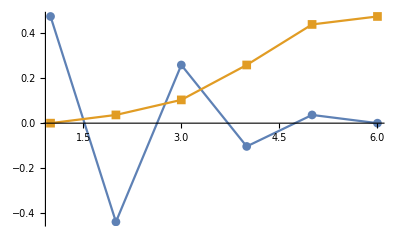

0.406319678854295201

```mathematica
ClearAll@searchCoinParameters`Cache;
target=spinCoherentState[5/2,Pi/4,0]+spinCoherentState[5/2,Pi-Pi/4,0+Pi]//N;
results=searchCoinParameters[5,Normalize@target,"IncludeProjectionInMaximization"->False,
WorkingPrecision->20,"CacheFinalExpression"->False
]
searchResultComputeProjectedOutput@results//normalizePhase//ListPlot[
{Re@#,Im@#},
PlotRange->All,
Joined->True,PlotMarkers->Automatic
]&
searchResultProjectionProbability@results
```

```mathematica
ClearAll@searchCoinParameters`Cache
target=spinCoherentState[5/2,1];
results=searchCoinParameters[Length@target-1,Normalize@target,"IncludeProjectionInMaximization"->False,
WorkingPrecision->20]
Echo[#,"Projection probability: "]&@searchResultProjectionProbability@results;
DynamicModule[{data=results},seeEvolutionByStep@results]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→0.999999999787851368,CoinParameters→{θ[1]→-0.78535295638787036552,ξ[1]→0.00029424264431544021113,θ[2]→0.44711344902695403867,ξ[2]→-1.5711135694358640648,θ[3]→2.0246396588529018239,ξ[3]→4.7127738325664227035,θ[4]→-1.1169144549785132312,ξ[4]→-1.5712294147789976986,θ[5]→-0.44717946262222734563,ξ[5]→1.5710091380134211227},TargetState→{1/(4 √2),(√(5/2))/4,(√5)/4,(√5)/4,(√(5/2))/4,1/(4 √2)}|>

Projection probability:  0.19541369926727736